# When Less is More Figure 4

## Preamble

```mathematica
$Version
```

```mathematica
Clear["Global`*"]
```

"When less is more: evolving large neural networks from small ones", 
Anil Radhakrishnan, John F . Lindner, Scott T . Miller, Sudeshna Sinha, William L . Ditto
2024 October 6

## Network

### Parameters

```mathematica
randomSeed=228;
```

```mathematica
nSkip=4;
nTrainData=32; (* number of training pairs *)
nTestData=nTrainData/nSkip;(* number of test pairs *)
```

```mathematica
nEpochs=2 10^4; (* number of training rounds *)
nTrials=10^4;(* number of trials *)
η=0.001; (* learning rate *)
```

```mathematica
nH=9; (* maximum number of neurons in the hidden layer *)
(* Ν0 e {0,1,2,...,nH}; initial network size *)
Ν∞=5; (* desired final network size *)
δn=1;(* add or delete step size *)
λ=0.1; (* loss size coupling *)
```

```mathematica
SeedRandom[randomSeed]; (* not working exactly, perhaps due to compiling? *)
```

### Gradual Step Function

```mathematica
θ[n_]:=Piecewise[{{0, n<0}, {Sin[(π n)/(2δn)]^2, 0<=n<=δn}, {1, δn<n}}]
```

### Static Activation Function

```mathematica
σ[z_]:=Tanh[z]
```

### Target Function: Bessel J_0+J_1+J_2

```mathematica
fRaw[x_]:=BesselJ[0,x]+BesselJ[1,x]+BesselJ[2,x]
```

```mathematica
xMin=-2π;xMax=2π;
fMin = NMinimize[{fRaw[x], xMin< x < xMax}, x][[1]];
fMax = NMaximize[{fRaw[x], xMin < x < xMax}, x][[1]]; 
f[x_]=Rescale[fRaw[Rescale[x,{-1, 1},{xMin, xMax}]],{fMin, fMax},{-1, 1}]
```

```mathematica
plotTarget=Plot[f[x],{x,-1,1},Frame->True,PlotRangePadding->None,PlotRange->{-1,1},AspectRatio->1,PlotStyle->Black,ImageSize->Small]
```

### Target Function: Cubic

```mathematica
g[x_]:=a x^3+b x^2+c x+d
```

```mathematica
s=Solve[{g[-1]==1,g[1]==1,g[1/3]==-2/3,g'[1/3]==0},{a,b,c,d},Reals][[1]];
```

```mathematica
f[x_]=g[x]/.s
```

```mathematica
Plot[f[x],{x,-1,1},PlotRange->{{-1,1},{-1,1}},Frame->True,AspectRatio->1,ImageSize->Small]
```

### Target Function: Cubic 2

```mathematica
g[x_]:=a x^3+b x^2+c x+d
```

```mathematica
s=Solve[{g[-1]==-1,g[1]==-1,g[1/3]==2/3,g'[1/3]==0},{a,b,c,d},Reals][[1]];
```

```mathematica
f[x_]=g[x]/.s
```

```mathematica
Plot[f[x],{x,-1,1},PlotRange->{{-1,1},{-1,1}},Frame->True,AspectRatio->1,ImageSize->Small]
```

### Target Function: Quadratic

```mathematica
h[x_]:=a x^2+b x+c
```

```mathematica
s=Solve[{h[-1]==1,h[1]==-1,h[0]==-1/5},{a,b,c},Reals][[1]];
```

```mathematica
f[x_]=h[x]/.s
```

```mathematica
Plot[f[x],{x,-1,1},PlotRange->{{-1,1},{-1,1}},Frame->True,AspectRatio->1,ImageSize->Small]
```

### Target Function: Quadratic 2

```mathematica
h[x_]:=a x^2+b x+c
```

```mathematica
s=Solve[{h[-1]==1,h[1]==-1/2,h'[1/2]==0},{a,b,c},Reals][[1]];
```

```mathematica
f[x_]=h[x]/.s
```

```mathematica
4f[x]//Simplify
```

```mathematica
Plot[f[x],{x,-1,1},PlotRange->{{-1,1},{-1,1}},Frame->True,AspectRatio->1,ImageSize->Small,PlotStyle->Black,FrameStyle->Directive[Black]]
```

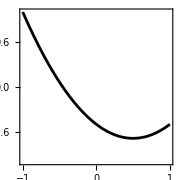

### Example Training Data

```mathematica
trainingPairs={#,f[#]}&/@RandomReal[{-1,1},nTrainData];
testingPairs={#,f[#]}&/@RandomReal[{-1,1},nTestData];
```

```mathematica
Length/@{trainingPairs,testingPairs}
```

```mathematica
pSize=0.02;trainingPairsPlot=ListPlot[trainingPairs,Frame->True,PlotRangePadding->None,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->Directive[PointSize[pSize],Blue],FrameTicksStyle->19,FrameStyle->18,LabelStyle->{FontFamily->"CMU Serif",Black}];
testingPairsPlot=ListPlot[testingPairs,Frame->True,PlotRangePadding->None,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->Directive[PointSize[pSize],Red],FrameTicksStyle->19,FrameStyle->18,LabelStyle->{FontFamily->"CMU Serif",Black}];
dataPlot=Show[trainingPairsPlot,testingPairsPlot]
```

### Weights & Biases

```mathematica
bVec[2]=Array[b[2],{nH}];
bVec[3]=Array[b[3],{1}];
```

```mathematica
wMat[2]=Array[w[2],{nH,2}];
wMat[3]=Array[w[3],{1,nH}];
```

### Neuronal Network

```mathematica
yHat[x_]=b[3][1]+∑_(m=1)^nH w[3][1,m]θ[Ν-m+1]σ[b[2][m]+Ν w[2][m,1]+x w[2][m,2]];
```

### Weights & Biases

```mathematica
wb={Ν,Table[{wMat[n],bVec[n]},{n,2,3}]}//Flatten;
```

### Mean Square Error

```mathematica
L0[{x_,y_}]=(y-yHat[x])^2;(* square error *)
```

```mathematica
xyTrainData=Table[{x[n],y[n]},{n,nTrainData}];
xyTestData=Table[{x[n],y[n]},{n,nTestData}];
```

```mathematica
LTrain=Mean[L0/@xyTrainData]+λ(Ν-Ν∞)^2;(* for batch gradient descent *)
LTest=Mean[L0/@xyTestData]+λ(Ν-Ν∞)^2;
```

### Gradients

```mathematica
dLTraindWb=D[LTrain,{wb}];(* Jacobian matrix *)
dLTestdWb=D[LTest,{wb}];(* Jacobian matrix *)
```

### Compile

#### Define

```mathematica
wbxyTrain={wb,xyTrainData}//Flatten;
wbxyTest={wb,xyTestData}//Flatten;
```

```mathematica
LTrainC=Compile[{#,_Real}&/@wbxyTrain//Evaluate,LTrain//Evaluate];
LTestC=Compile[{#,_Real}&/@wbxyTest//Evaluate,LTest//Evaluate];
```

```mathematica
dLTraindWbC=Compile[{#,_Real}&/@wbxyTrain//Evaluate,dLTraindWb//Evaluate];
dLTestdWbC=Compile[{#,_Real}&/@wbxyTest//Evaluate,dLTestdWb//Evaluate];
```

#### Test

```mathematica
wbxyTrainDummy=RandomReal[{-1,1},Length@wbxyTrain];
wbxyTestDummy=RandomReal[{-1,1},Length@wbxyTest];
```

```mathematica
LTrainC@@wbxyTrainDummy==LTrain/.Thread[wbxyTrain->wbxyTrainDummy]
LTestC@@wbxyTestDummy==LTest/.Thread[wbxyTest->wbxyTestDummy]
```

```mathematica
(dLTraindWbC@@wbxyTrainDummy-dLTraindWb/.Thread[wbxyTrain->wbxyTrainDummy])//Chop//Union
(dLTestdWbC@@wbxyTestDummy-dLTestdWb/.Thread[wbxyTest->wbxyTestDummy])//Chop//Union
```

## Probability Distributions

### Final Test Loss

```mathematica
computeFinalTestLoss[Ν0_]:=
Module[{wbxyTrainData,wbxyTestData,LTrainHistory,LTestHistory,e},
wbxyTrainData={
Ν0, (* Subscript[w^1, 11] *)
RandomReal[{-1,1},Length@wb-1], (* other weights & biases *)
{#,f[#]}&/@RandomReal[{-1,1},nTrainData](* training pairs *)
}//Flatten;
wbxyTestData={
ConstantArray[0,Length@wb], (* dummy data *)
{#,f[#]}&/@RandomReal[{-1,1},nTestData](* testing pairs *)
}//Flatten;

For[ e=1,e<=nEpochs,e++, (* batch gradient descent *)
wbxyTrainData[[1;;Length@wb]]-=η dLTraindWbC@@wbxyTrainData 
];

wbxyTestData[[1;;Length@wb]]=wbxyTrainData[[1;;Length@wb]];
LTestC@@wbxyTestData (* report final loss on untrained test data *)
]
```

### Acquire Data

#### N=0 Growing

```mathematica
AbsoluteTiming[
LFinals0=ParallelTable[computeFinalTestLoss[0],{n,nTrials}];
][[1]]seconds
```

#### N=5 Grown

```mathematica
AbsoluteTiming[
LFinals5=ParallelTable[computeFinalTestLoss[5],{n,nTrials}];
][[1]]seconds
```

### Histograms

```mathematica
LFinals05=Join[LFinals0,LFinals5];
```

```mathematica
{log10Min,log10Max}={Floor@Log10@Min@LFinals05,Ceiling@Log10@Max@LFinals05}
```

```mathematica
{mean0,mean5}=Mean/@{LFinals0,LFinals5}
```

```mathematica
mean5/mean0
```

```mathematica
Histogram[{LFinals0,LFinals5},{"Log",{0.1}},"Probability",Frame->True,BarOrigin->Bottom,AspectRatio->1,ImageSize->220,PlotLabel->" ",PlotRange->{{10^log10Min,10^log10Max},{0,All}},FrameTicks->{{Automatic,None},{Table[{10^n,Superscript[10,n]},{n,log10Min,log10Max}],None}},FrameStyle->Directive[14,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[12,FontFamily->"CMU Serif",Black],GridLines->{10^-4 Automatic}]
```

```mathematica
dx=0.1;aRatio=0.36;
{bins,heights}=HistogramList[LFinals05,{"Log",{dx}},"Probability"];
xRange={10^log10Min,10^log10Max};
(*xRange={10^-2,10^log10Max};*)
yMin=10^-4;yMax=Ceiling[Max@heights,0.1]; yRange={yMin,yMax};
histogramPlot0=Histogram[LFinals0,{"Log",{dx}},"Probability",ScalingFunctions->{"Log","Log"},Frame->True,BarOrigin->Bottom,AspectRatio->aRatio,ImageSize->220,PlotLabel->" ",PlotRange->{xRange,yRange},FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-5,-1}],None},{None,Table[{10^n,Superscript[10,n]},{n,log10Min,log10Max,2}]}},FrameLabel->{{"↑ρ",None},{None,"final growing StyleBox[\"L\",FontSlant->\"Italic\"]"}},RotateLabel->False,FrameStyle->Directive[21,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[15,FontFamily->"CMU Serif",Black],ChartStyle->Directive[EdgeForm[None],Cyan],GridLines->{{mean0},None},Method->{"GridLinesInFront"->True},GridLinesStyle->Directive[Thickness[0.01],Red]
];
histogramPlot5=Histogram[LFinals5,{"Log",{dx}},"Probability",ScalingFunctions->{"Log","Log"},Frame->True,BarOrigin->Top,AspectRatio->aRatio,ImageSize->220,PlotLabel->" ",PlotRange->{xRange,yRange},FrameTicks->{{Rest@Table[{10^n,Superscript[10,n]},{n,-5,-1}],None},{Table[{10^n,Superscript[10,n]},{n,log10Min,log10Max,2}],None}},FrameLabel->{{"↓ρ",None},{"final grown StyleBox[\"L\",FontSlant->\"Italic\"]",None}},RotateLabel->False,FrameStyle->Directive[21,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[15,FontFamily->"CMU Serif",Black],ChartStyle->Directive[EdgeForm[None],Darker@Blue],GridLines->{{mean5},None},Method->{"GridLinesInFront"->True},GridLinesStyle->Directive[Thickness[0.01],Red]
];
GraphicsColumn[{histogramPlot0,histogramPlot5},Spacings->{0,{0,-40.5,0}},ImageSize->400]
```